```mathematica
ClearAll["Global`*"]
coordenadasU:={t,r,θ,ϕ,γ}
len:=Length[coordenadasU]
g={{-NN[r]^2*f[r],0,0,0,0},{0,1/f[r],0,0,0},{0,0,r^2,0,0},{0,0,0,r^2*Sin[θ]^2,0},{0,0,0,0,r^2*Sin[θ]^2*Sin[ϕ]^2}};
ginv=Inverse[g];
nn={{-1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
detg:=Assuming[NN[r]>0&&r>0&&Sin[θ]^4>0&&Sin[ϕ]>0,Simplify[Sqrt[-Det[g]]/(Sin[θ]^2*Sin[ϕ])]]
r1={x[0]->t};
r2={x[1]->r};
r3={x[2]->θ};
r4={x[3]->ϕ};
r5={x[4]->γ};
```

### Métrica

```mathematica
For[j=0,j<len,j++,For[i=0,i<len,i++,gdown[i,j]=g⟦i+1⟧⟦j+1⟧;]]
For[j=0,j<len,j++,For[i=0,i<len,i++,gup[i,j]=ginv⟦i+1⟧⟦j+1⟧;]]
```

### Símbolos de Christoffel

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[ρ=0,ρ<len,ρ++,
Γ[ρ,μ,ν]=Series[1/2 *Sum[gup[ρ,σ] (D[gdown[ν,σ],x[μ]/.r1/.r2/.r3/.r4/.r5]+D[gdown[σ,μ],x[ν]/.r1/.r2/.r3/.r4/.r5]-D[gdown[μ,ν],x[σ]/.r1/.r2/.r3/.r4]/.r5),{σ,0,len-1}],{ϵ,0,2}];
]
]
]
```

### Riemann’s Tensor

RUDDD

```mathematica
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUDDD[ρ,σ,μ,ν]=Simplify[D[Γ[ρ,σ,ν],x[μ]/.r1/.r2/.r3/.r4/.r5]-D[Γ[ρ,σ,μ],x[ν]/.r1/.r2/.r3/.r4/.r5]+Sum[Γ[ρ,λ,μ]* Γ[λ,σ,ν],{λ,0,len-1}]-Sum[Γ[ρ,λ,ν]* Γ[λ,σ,μ],{λ,0,len-1}]];
]
]
]
]
```

RDDDD

```mathematica
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemDDDD[μ,ν,ρ,σ]=Sum[gdown[μ,ψ]*RiemUDDD[ψ,ν,ρ,σ],{ψ,0,len-1}]
]
]
]
]
```

RUUUD

```mathematica
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUUD[μ,ν,ρ,σ]=Sum[gdown[σ,ψ]*RiemUUUU[μ,ν,ρ,ψ],{ψ,0,len-1}]
]
]
]
]
```

RDDDU

```mathematica
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemDDDU[μ,ν,ρ,σ]=Sum[gup[σ,ψ]*RiemDDDD[μ,ν,ρ,ψ],{ψ,0,len-1}]
]
]
]
]
```

RUUUU

```mathematica
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUUU[μ,ν,ρ,σ]=Sum[gup[σ,φ]*gup[ν,β]*gup[ρ,ψ]*RiemUDDD[μ,β,ψ,φ],{φ,0,len-1},{ψ,0,len-1},{β,0,len-1}]
]
]
]
]
```

RUUDD

```mathematica
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUDD[μ,ν,ρ,σ]=Sum[gup[ν,ψ]*RiemUDDD[μ,ψ,ρ,σ],{ψ,0,len-1}]
]
]
]
]
```

RUDUD

```mathematica
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUDUD[μ,ν,ρ,σ]=Sum[gup[ρ,ψ]*RiemUDDD[μ,ν,ψ,σ],{ψ,0,len-1}]
]
]
]
]
```

### Ricci’s Tensor

RDD

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RDD[μ,ν]=Expand[Simplify[Sum[RiemDDDU[μ,ρ,ν,ρ],{ρ,0,len-1}]]];
]
]
```

RUU

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RUU[μ,ν]=Expand[Simplify[Sum[gup[μ,α]*gup[ν,β]*RDD[α,β],{α,0,len-1},{β,0,len-1}]]];
]
]
```

RUD

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RUD[μ,ν]=Expand[Simplify[Sum[gup[μ,α]*RDD[α,ν],{α,0,len-1}]]];
]
]
```

RDU

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RDU[μ,ν]=Expand[Simplify[Sum[gup[ν,α]*RDD[μ,α],{α,0,len-1}]]];
]
]
```

### Scalar Tensor

```mathematica
ClearAll[μ,ν]
R=Expand[Simplify[Sum[Sum[gup[μ,ν] RDD[μ,ν],{μ,0,len-1}],{ν,0,len-1}]]];
```

## Curvatura n=1

```mathematica
L[1]=Collect[Expand[R],{NN[r],NN'[r],NN''[r]}]
S[1]:=Collect[-Expand[R],{NN[r],NN'[r],NN''[r]}]
Z[1]:=Collect[-Expand[R],{NN[r],NN'[r],NN''[r]}]
```

6/r^2-(6 f[r])/r^2-(6 f'[r])/r-f''[r]+((-(6 f[r])/r-3 f'[r]) NN'[r]-2 f[r] NN''[r])/NN[r]

## Curvatura n=2

```mathematica
L[2]=Collect[Simplify[R^2-4*Sum[RDD[μ,ν]*RUU[μ,ν],{μ,0,len-1},{ν,0,len-1}]+Sum[RiemDDDD[μ,ν,σ,γ]*RiemUUUU[μ,ν,σ,γ],{μ,0,len-1},{ν,0,len-1},{σ,0,len-1},{γ,0,len-1}]],{NN[r],NN'[r],NN''[r]}]
S[2]:=Collect[Simplify[(-5/24)*(R^2-4*Sum[RDD[μ,ν]*RUU[μ,ν],{μ,0,len-1},{ν,0,len-1}]+Sum[RiemDDDD[μ,ν,σ,γ]*RiemUUUU[μ,ν,σ,γ],{μ,0,len-1},{ν,0,len-1},{σ,0,len-1},{γ,0,len-1}])],{NN[r],NN'[r],NN''[r]}]
Z[2]:=Collect[Simplify[(-1/6)*(R^2-4*Sum[RDD[μ,ν]*RUU[μ,ν],{μ,0,len-1},{ν,0,len-1}]+Sum[RiemDDDD[μ,ν,σ,γ]*RiemUUUU[μ,ν,σ,γ],{μ,0,len-1},{ν,0,len-1},{σ,0,len-1},{γ,0,len-1}])],{NN[r],NN'[r],NN''[r]}]
```

(12 (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r]))/r^3+((12 (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r])) NN'[r])/r^3+(12 (-2 r f[r]+2 r f[r]^2) NN''[r])/r^3)/NN[r]

## Curvatura n=3

```mathematica
I1:=Simplify[Sum[RiemUDUD[c,a,d,b]*RiemUDUD[e,c,h,d]*RiemUDUD[a,e,b,h],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1},{h,0,len-1}]]
I2:=Simplify[Sum[RiemUUDD[c,d,a,b]*RiemUUDD[e,h,c,d]*RiemUUDD[a,b,e,h],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1},{h,0,len-1}]]
I3:=Simplify[Sum[RiemDDDD[a,b,c,d]*RiemUUUD[a,b,c,e]*RUU[d,e],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1}]]
I4:=Simplify[Sum[RiemDDDD[a,b,c,d]*RiemUUUU[a,b,c,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}]*R]
I5:=Simplify[Sum[RiemDDDD[a,b,c,d]*RUU[a,c]*RUU[b,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}]]
I6:=Simplify[Sum[RUD[a,b]*RUD[b,c]*RUD[c,a],{a,0,len-1},{b,0,len-1},{c,0,len-1}]]
I7:=Simplify[Sum[RUD[a,b]*RUD[b,a],{a,0,len-1},{b,0,len-1}]*R]
I8:=Simplify[R^3]
```

### Coeficientes GQTG

```mathematica
Clear[c1,c2,c3,c4,c5,c6,c7,c8]
```

```mathematica
L3coef=Simplify[(L[1]+L[2]+c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)*detg/.NN[r]->1/.NN'[r]->0/.NN''[r]->0/.NN'''[r]->0]
```

-1/(8 r^3)(-48 r^4+48 r^4 f[r]+48 r^5 f'[r]+8 r^6 f''[r]+8 c8 (-6+6 f[r]+6 r f'[r]+r^2 f''[r])^3-96 r^3 (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+8 c4 (-6+6 f[r]+6 r f'[r]+r^2 f''[r]) (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+8 c2 (24 (-1+f[r])^3+6 r^3 f'[r]^3+r^6 f''[r]^3)-2 c7 (6-6 f[r]-6 r f'[r]-r^2 f''[r]) (12 (-2+2 f[r]+r f'[r])^2+2 r^2 (3 f'[r]+r f''[r])^2)+c6 (24 (-2+2 f[r]+r f'[r])^3+2 r^3 (3 f'[r]+r f''[r])^3)-6 c1 (8+24 f[r]^2-8 f[r]^3-12 f[r] (2+r^2 f'[r]^2)-3 r^2 f'[r]^2 (-4+r^2 f''[r]))-4 c3 (48-48 f[r]^3-15 r^3 f'[r]^3-24 f[r]^2 (-6+r f'[r])-12 f[r] (12-4 r f'[r]+r^2 f'[r]^2)-r^6 f''[r]^3-3 r^2 f'[r]^2 (-4+r^2 f''[r])-3 r f'[r] (8+r^4 f''[r]^2))-2 c5 (96-96 f[r]^3-36 r^3 f'[r]^3-96 f[r]^2 (-3+r f'[r])-r^6 f''[r]^3+f'[r]^2 (96 r^2-21 r^4 f''[r])-6 r f'[r] (16-4 r^2 f''[r]+r^4 f''[r]^2)-24 f[r] (12+4 r^2 f'[r]^2+r f'[r] (-8+r^2 f''[r]))))

```mathematica
vars={f[r],Derivative[1][f][r],Derivative[2][f][r],Derivative[3][f][r],Derivative[4][f][r],Derivative[5][f][r]};
monomios=DeleteDuplicates@Join[Select[Times@@@Subsets[vars,{2}],UnsameQ@@List@@#&],(*productos cruzados*)Power@@@Tuples[{vars,{2}}]  (*potencias cuadradas*)];
monomiosOrdenados=Join[monomios,vars];
```

```mathematica
monomiosOrdenados
```

{f[r] f'[r],f[r] f''[r],f[r] f^(3)[r],f[r] f^(4)[r],f[r] f^(5)[r],f'[r] f''[r],f'[r] f^(3)[r],f'[r] f^(4)[r],f'[r] f^(5)[r],f''[r] f^(3)[r],f''[r] f^(4)[r],f''[r] f^(5)[r],f^(3)[r] f^(4)[r],f^(3)[r] f^(5)[r],f^(4)[r] f^(5)[r],f[r]^2,f'[r]^2,f''[r]^2,(f^(3)[r])^2,(f^(4)[r])^2,(f^(5)[r])^2,f[r],f'[r],f''[r],f^(3)[r],f^(4)[r],f^(5)[r]}

```mathematica
EulerLagrange:=Collect[Expand[D[L3coef,f[r]]-D[D[L3coef,f'[r]],r]+D[D[L3coef,f''[r]],{r,2}]],monomiosOrdenados]
```

```mathematica
For[i=1,i<=Length[monomiosOrdenados],i++,eq[i]=Coefficient[EulerLagrange,monomiosOrdenados[[i]]]==0/.f[r]->0/.f'[r]->0/.f''[r]->0/.f'''[r]->0/.f''''[r]->0]
```

```mathematica
eq[0]:=-(18 c1)/r^3-(72 c2)/r^3-(96 c3)/r^3-(384 c4)/r^3-(120 c5)/r^3-(144 c6)/r^3-(528 c7)/r^3-(2160 c8)/r^3==0
```

```mathematica
Simplify[Solve[{eq[0],eq[1],eq[2],eq[3],eq[4],eq[5],eq[6],eq[7],eq[8],eq[9],eq[10],eq[11],eq[12],eq[13],eq[14],eq[15],eq[16],eq[17],eq[18],eq[19],eq[20],eq[21],eq[22],eq[23],eq[24],eq[25],eq[26],eq[27]},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c1→1/3 (10 c3+124 c4+13 c7),c2→-c3/6+c4+c7/4,c5→-2 c3-20 c4-3 c7,c6→2/3 (c3+20 c4+c7),c8→1/6 (-2 c4-c7)}}

```mathematica
eq1:=c1==1/3 (10 c3+124 c4+13 c7)
eq2:=c2==-c3/6+c4+c7/4
eq3:=c5==-2 c3-20 c4-3 c7
eq4:=c6==2/3 (c3+20 c4+c7)
eq5:=c8==1/6 (-2 c4-c7)
```

```mathematica
Simplify[Solve[{eq1,eq2,eq3,eq4,eq5},{c4,c5,c6,c7,c8}]]
```

{{c4→1/216 (9 c1-156 c2-56 c3),c5→1/27 (-9 c1-168 c2-52 c3),c6→2/81 (18 c1-204 c2-67 c3),c7→1/54 (-9 c1+372 c2+92 c3),c8→1/648 (9 c1-588 c2-128 c3)}}

```mathematica
Clear[c3]
c4:=1/216 (9 c1-156 c2-56 c3)
c5:=1/27 (-9 c1-168 c2-52 c3)
c6:=2/81 (18 c1-204 c2-67 c3)
c7:=1/54 (-9 c1+372 c2+92 c3)
c8:=1/648 (9 c1-588 c2-128 c3)
```

```mathematica
S[3]=Collect[Simplify[(c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)*detg/.c1->14/.c2->0/.c3->2],{NN[r],NN'[r],NN''[r]}]
```

-1/(27 r^3)4 NN[r] (-244+244 f[r]^3-175 r^3 f'[r]^3-54 r^2 f''[r]-6 f[r]^2 (122+52 r f'[r]+9 r^2 f''[r])+12 r f'[r] (-26+35 r^2 f''[r])+3 r^2 f'[r]^2 (36+35 r^2 f''[r])-12 f[r] (-61+9 r^2 f'[r]^2-9 r^2 f''[r]+r f'[r] (-52+35 r^2 f''[r])))-1/(27 r^3)4 NN'[r] (-312 r f[r]^3+9 r^2 f'[r] (-18+140 r f'[r]+35 r^2 f'[r]^2)-6 r f[r]^2 (-104+63 r f'[r]+70 r^2 f''[r])+3 r f[r] (-595 r^2 f'[r]^2+10 r f'[r] (18+7 r^2 f''[r])+4 (-26+35 r^2 f''[r])))-(4 (-108 r^2 f[r]^3-24 r^2 f[r]^2 (-9+35 r f'[r])+6 r^2 f[r] (-18+140 r f'[r]+35 r^2 f'[r]^2)) NN''[r])/(27 r^3)+(-(4 NN'[r]^2 (210 r^3 (6-7 f[r]) f[r] f'[r]+630 r^4 f[r] f'[r]^2+210 r^4 f[r]^2 f''[r]))/(27 r^3)-(4 (-840 r^3 (-1+f[r]) f[r]^2+420 r^4 f[r]^2 f'[r]) NN'[r] NN''[r])/(27 r^3))/NN[r]+(-(4 (140 r^3 f[r]^3+630 r^4 f[r]^2 f'[r]) NN'[r]^3)/(27 r^3)-560/9 r f[r]^3 NN'[r]^2 NN''[r])/NN[r]^2

### Coeficientes quasi-topológicos

```mathematica
L[3]=Collect[Simplify[(L[1]+L[2]+c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)*detg],{NN[r],NN'[r],NN''[r]}]
```

1/(27 r^3)NN[r] (72 c1+48 c2-16 c3+162 r^4-8 (9 c1+6 c2-2 c3) f[r]^3+5 (9 c1+60 c2+7 c3) r^3 f'[r]^3+648 c2 r^2 f''[r]+108 c3 r^2 f''[r]-324 r^4 f''[r]-27 r^6 f''[r]+12 f[r]^2 (2 (9 c1+6 c2-2 c3)+(9 c1-48 c2-11 c3) r f'[r]+9 (6 c2+c3) r^2 f''[r])-3 r^2 f'[r]^2 (36 (12 c2+2 c3-3 r^2)+(9 c1+60 c2+7 c3) r^2 f''[r])-6 r f'[r] (-18 c1+96 c2+22 c3+108 r^2+27 r^4+2 (9 c1+60 c2+7 c3) r^2 f''[r])+6 f[r] (-36 c1-24 c2+8 c3-27 r^4+36 (6 c2+c3) r^2 f'[r]^2+18 r^2 (-12 c2-2 c3+3 r^2) f''[r]+2 r f'[r] (-18 c1+96 c2+22 c3+54 r^2+(9 c1+60 c2+7 c3) r^2 f''[r])))+1/(27 r^3)NN'[r] (12 (9 c1-48 c2-11 c3) r f[r]^3-9 r^2 f'[r] (9 (-24 c2-4 c3+12 r^2+r^4)+4 (9 c1+60 c2+7 c3) r f'[r]+(9 c1+60 c2+7 c3) r^2 f'[r]^2)+12 r f[r]^2 (-18 c1+96 c2+22 c3+54 r^2+63 (6 c2+c3) r f'[r]+(9 c1+60 c2+7 c3) r^2 f''[r])-3 r f[r] (-36 c1+192 c2+44 c3+216 r^2+54 r^4-17 (9 c1+60 c2+7 c3) r^2 f'[r]^2+4 (9 c1+60 c2+7 c3) r^2 f''[r]+2 f'[r] (90 r (12 c2+2 c3-3 r^2)+(9 c1+60 c2+7 c3) r^3 f''[r])))+1/(27 r^3)(216 (6 c2+c3) r^2 f[r]^3+24 r^2 f[r]^2 (-9 (12 c2+2 c3-3 r^2)+(9 c1+60 c2+7 c3) r f'[r])-6 r^2 f[r] (9 (-24 c2-4 c3+12 r^2+r^4)+4 (9 c1+60 c2+7 c3) r f'[r]+(9 c1+60 c2+7 c3) r^2 f'[r]^2)) NN''[r]+((NN'[r]^2 (-6 (9 c1+60 c2+7 c3) r^3 (6-7 f[r]) f[r] f'[r]-18 (9 c1+60 c2+7 c3) r^4 f[r] f'[r]^2-6 (9 c1+60 c2+7 c3) r^4 f[r]^2 f''[r]))/(27 r^3)+((24 (9 c1+60 c2+7 c3) r^3 (-1+f[r]) f[r]^2-12 (9 c1+60 c2+7 c3) r^4 f[r]^2 f'[r]) NN'[r] NN''[r])/(27 r^3))/NN[r]+(((-4 (9 c1+60 c2+7 c3) r^3 f[r]^3-18 (9 c1+60 c2+7 c3) r^4 f[r]^2 f'[r]) NN'[r]^3)/(27 r^3)-4/9 (9 c1+60 c2+7 c3) r f[r]^3 NN'[r]^2 NN''[r])/NN[r]^2

```mathematica
vars2={f[r],Derivative[1][f][r],Derivative[2][f][r]};
monomios2=DeleteDuplicates@Flatten[Table[(*Genero todas las tuplas de longitud "deg",convierto repeticiones en potencias*)Times@@(Power@@@Tally[#])&/@Tuples[vars2,deg],{deg,1,3}],1];
```

```mathematica
monomiosOrdenados2=Join[monomios2,{f[r]*f'[r]*f''[r]}]
monomiosN={NN'[r]^2,NN'[r]NN''[r],NN'[r]^3,NN'[r]^2NN''[r]}
```

{f[r],f'[r],f''[r],f[r]^2,f[r] f'[r],f[r] f''[r],f'[r]^2,f'[r] f''[r],f''[r]^2,f[r]^3,f[r]^2 f'[r],f[r]^2 f''[r],f[r] f'[r]^2,f[r] f'[r] f''[r],f[r] f''[r]^2,f'[r]^3,f'[r]^2 f''[r],f'[r] f''[r]^2,f''[r]^3,f[r] f'[r] f''[r]}

{NN'[r]^2,NN'[r] NN''[r],NN'[r]^3,NN'[r]^2 NN''[r]}

```mathematica
For[i=1,i<=Length[monomiosN],i++,
For[j=1,j<=Length[monomiosOrdenados2],j++,
ec[i][j]=Coefficient[Coefficient[L[3],monomiosN[[i]]],monomiosOrdenados2[[j]]]==0/.f[r]->0/.f'[r]->0/.f''[r]->0/.NN'[r]->0/.NN''[r]->0/.NN[r]->1]]
lista=DeleteCases[Flatten[Table[ec[i][j],{i,1,Length[monomiosN]},{j,1,Length[monomiosOrdenados2]}]],True]
```

{-12 c1-80 c2-(28 c3)/3==0,14 c1+(280 c2)/3+(98 c3)/9==0,-2 c1 r-(40 c2 r)/3-(14 c3 r)/9==0,-6 c1 r-40 c2 r-(14 c3 r)/3==0,(-216 c1 r^3-1440 c2 r^3-168 c3 r^3)/(27 r^3)==0,(216 c1 r^3+1440 c2 r^3+168 c3 r^3)/(27 r^3)==0,-4/9 (9 c1+60 c2+7 c3) r==0,-(4 c1)/3-(80 c2)/9-(28 c3)/27==0,-6 c1 r-40 c2 r-(14 c3 r)/3==0,-4/9 (9 c1+60 c2+7 c3) r==0}

```mathematica
Solve[lista,{c1,c2,c3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c3→-(9 c1)/7-(60 c2)/7}}

```mathematica
c3:=-(9 c1)/7-(60 c2)/7
```

```mathematica
Simplify[{c3,c4,c5,c6,c7,c8}]
```

{-3/7 (3 c1+20 c2),3/8 (c1+4 c2),3/7 (5 c1+24 c2),2/7 (9 c1+32 c2),-3/14 (11 c1+36 c2),1/56 (15 c1+44 c2)}

Densidad lagrangiana quasi-topológica

```mathematica
Z[3]=Simplify[(c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)/.c1->1/.c2->0]
Zalt[3]:=Simplify[(c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)/.c1->0/.c2->1]
```

-1/(7 r^6 NN[r])12 (-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))

```mathematica
X6=Simplify[4*I2-8*I1-24*I3+3*I4+24*I5+16*I6-12*I7+I8]
```

0

```mathematica
Simplify[2*Z3-Zalt3]
```

2 Z3-Zalt3

```mathematica
Xalt6=Simplify[(c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)/.c1->-8/.c2->4]
```

0

```mathematica
Zgeneral[3]:=Simplify[(c1*I1+c2*I2+c3*I3+c4*I4+c5*I5+c6*I6+c7*I7+c8*I8)/.c1->β/.c2->0]
```

## Soluciones de 3er orden en la curvatura

### Solución Quasi-topológica

```mathematica
L=Collect[Simplify[-(Z[1]+α*Z[2]+α^2*Z[3])*detg],{NN[r],NN'[r],NN''[r]}]
```

(-(72 α^2 (-1+f[r]) f[r]^2)/(7 r^2)-(108 α^2 (-1+f[r]) f'[r])/(7 r)-3 r^2 (2 f[r]+r f'[r])+(36 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/(7 r^2)+2 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r]))) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r]+2 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+(12 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))/(7 r^3))+(-2 r^3 f[r]+4 r α (-1+f[r]) f[r]-(72 α^2 (-1+f[r]) f[r])/(7 r)+(72 α^2 (-1+f[r]) f[r]^2)/(7 r)) NN''[r]

```mathematica
Fprim0:=Coefficient[L,NN[r]]
F1:=Coefficient[L,NN'[r]]
F2:=Coefficient[L,NN''[r]]
```

```mathematica
ecs1=Simplify[Integrate[Fprim0,r]-F1+D[F2,r]]==c
```

(3 (7 r^4+4 α^2)-(21 r^4+14 r^2 α+36 α^2) f[r]+α (7 r^2+36 α) f[r]^2-12 α^2 f[r]^3)/(7 r^2)==c

```mathematica
fz3=f[r]/. Solve[ecs1,f[r],Reals][[1]]
```

Root[7 c r^2-21 r^4-12 α^2+(21 r^4+14 r^2 α+36 α^2) #1+(-7 r^2 α-36 α^2) #1^2+12 α^2 #1^3&,1]

```mathematica
fz3=Expand[PowerExpand[Assuming[r>0&&α>0,Simplify[ToRadicals[fz3]]]]]
```

1+(7 r^2)/(36 α)-(101 7^(2/3) r^(10/3))/(36 α (-1085 r^4-1944 c α-1944 α^2+18 √3 √(8631 r^8+4340 r^4 α (c+α)+3888 α^2 (c+α)^2))^(1/3))+(7^(1/3) r^(2/3) (-1085 r^4-1944 c α-1944 α^2+18 √3 √(8631 r^8+4340 r^4 α (c+α)+3888 α^2 (c+α)^2))^(1/3))/(36 α)

```mathematica
f3red=Simplify[fz3/.r->Sqrt[36α/7]r2]
```

1+r2^2-(101 (2/7)^(1/3) (r2 √α)^(10/3))/(α (-147 c α-147 α^2-2170 r2^4 α^2+√21 √(α^2 (1029 c^2+98 c (21+310 r2^4) α+(1029+30380 r2^4+1597968 r2^8) α^2)))^(1/3))+((r2 √α)^(2/3) (-1944 c α-1944 α^2-(200880 r2^4 α^2)/7+648/7 √((4793904 r2^8 α^4)/7+13020 r2^4 α^3 (c+α)+441 α^2 (c+α)^2))^(1/3))/(6 6^(1/3) α)

```mathematica
α:=0.03
μ:=1
Plot[fz3,{r,0,2}]
Clear[α,μ]
```

-Graphics-

### Solución GQTG

```mathematica
LS=Collect[Simplify[-(S[1]+α*S[2]+α^2*S[3])*detg],{NN[r],NN'[r],NN''[r]}]
```

1/54 NN'[r]^2 (5040 r^3 α^2 f[r] f'[r] (2+r f'[r])+1680 r^3 α^2 f[r]^2 (-7 f'[r]+r f''[r]))+4/27 α^2 NN[r]^2 (-244+244 f[r]^3-175 r^3 f'[r]^3-54 r^2 f''[r]-6 f[r]^2 (122+52 r f'[r]+9 r^2 f''[r])+12 r f'[r] (-26+35 r^2 f''[r])+3 r^2 f'[r]^2 (36+35 r^2 f''[r])-12 f[r] (-61+9 r^2 f'[r]^2-9 r^2 f''[r]+r f'[r] (-52+35 r^2 f''[r])))+1/54 (-54 r (2 r^2+5 α) f[r]+270 r α f[r]^2) NN''[r]+NN'[r] (1/54 (270 α f[r]^2-81 r (2 r^2+5 α) f'[r]+9 f[r] (-36 r^2-30 α+75 r α f'[r]))+1/54 (-6720 r^3 α^2 f[r]^3+3360 r^3 α^2 f[r]^2 (2+r f'[r])) NN''[r])+NN[r] (1/54 (324 r-324 r f[r]-324 r^2 f'[r]-270 α f'[r]+270 α f[r] f'[r]+135 r α f'[r]^2-27 r (2 r^2+5 α) f''[r]+135 r α f[r] f''[r])+1/54 NN'[r] (-2496 r α^2 f[r]^3-1296 r^2 α^2 f'[r]+10080 r^3 α^2 f'[r]^2-14280 r^3 α^2 f[r] f'[r]^2+2520 r^4 α^2 f'[r]^3+240 r^2 α^2 f[r] f'[r] (18+7 r^2 f''[r])+96 r α^2 f[r] (-26+35 r^2 f''[r])-48 r α^2 f[r]^2 (-104+63 r f'[r]+70 r^2 f''[r]))+1/54 (-864 r^2 α^2 f[r]-864 r^2 α^2 f[r]^3+6720 r^3 α^2 f[r] f'[r]+1680 r^4 α^2 f[r] f'[r]^2-192 r^2 α^2 f[r]^2 (-9+35 r f'[r])) NN''[r])+(1/54 (1120 r^3 α^2 f[r]^3+5040 r^4 α^2 f[r]^2 f'[r]) NN'[r]^3+560/9 r^4 α^2 f[r]^3 NN'[r]^2 NN''[r])/NN[r]

```mathematica
LS1:=LS/.NN[r]->1/.NN'[r]->0/.NN''[r]->0
Simplify[D[L1S,f[r]]-D[D[L1S,f'[r]],r]+D[D[L1S,f''[r]],{r,2}]]
```

0

```mathematica
Simplify[D[LS,f[r]]-D[D[LS,f'[r]],r]+D[D[LS,f''[r]],{r,2}]]
```

1/(18 NN[r]^2)(1680 r^4 α^2 f[r]^2 NN'[r]^4+24 α^2 NN[r]^4 (104 f[r]^2+35 r^2 f'[r]^2+70 r f'[r] (4+r^2 f''[r])+4 (26+35 r^2 f''[r])-4 f[r] (52+70 r f'[r]+35 r^2 f''[r]))-560 r^3 α^2 f[r]^2 NN[r] NN'[r]^2 (10 NN'[r]+3 r NN''[r])+NN[r]^2 NN'[r] (9 (6 r^2+5 α)-8 r^2 α^2 (-18+280 r f'[r]+175 r^2 f'[r]^2) NN'[r]+320 r^2 α^2 f[r]^2 (39 NN'[r]+14 r NN''[r])-α f[r] (45+16 r^2 α NN'[r] (264-175 r f'[r]+35 r^2 f''[r])+560 r^3 α (2+3 r f'[r]) NN''[r]))-8 r α^2 NN[r]^3 (NN'[r] (-68+836 f[r]^2+35 r^2 f'[r]^2+280 r^2 f''[r]+280 r^3 f'[r] f''[r]-6 f[r] (128+175 r f'[r]+105 r^2 f''[r]))+r ((18+18 f[r]^2+280 r f'[r]+175 r^2 f'[r]^2+f[r] (-36-350 r f'[r]+70 r^2 f''[r])) NN''[r]+70 r f[r] (2-2 f[r]+r f'[r]) NN^(3)[r])))

### Solución quasi-topológica general

```mathematica
Lgeneral=Collect[-(Z[1]+α*Z[2]+Zgeneral[3])*detg,{NN[r],NN'[r],NN''[r]}]
```

r^3 (-(6 f[r])/r-(72 β (-1+f[r]) f[r]^2)/(7 r^5)-3 f'[r]-(108 β (-1+f[r]) f'[r])/(7 r^4)+(36 β (-1+f[r]) f[r] (2+7 r f'[r]))/(7 r^5)+(2 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r])))/r^3) NN'[r]+r^3 NN[r] (6/r^2-(6 f[r])/r^2-(6 f'[r])/r-f''[r]+(2 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r]))/r^3+(12 β (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))/(7 r^6))+r^3 (-2 f[r]-(72 β (-1+f[r]) f[r])/(7 r^4)+(72 β (-1+f[r]) f[r]^2)/(7 r^4)+(2 α (-2 r f[r]+2 r f[r]^2))/r^3) NN''[r]

```mathematica
Fgenprim0:=Coefficient[Lgeneral,NN[r]]
Fgen1:=Coefficient[Lgeneral,NN'[r]]
Fgen2:=Coefficient[Lgeneral,NN''[r]]
```

```mathematica
Clear[c]
ecs2=Simplify[Integrate[Fgenprim0,r]-Fgen1+D[Fgen2,r]]==c
```

(3 (7 r^4+4 β)-(21 r^4+14 r^2 α+36 β) f[r]+(7 r^2 α+36 β) f[r]^2-12 β f[r]^3)/(7 r^2)==c

```mathematica
fzgen3=f[r]/. Solve[ecs2,f[r],Reals][[1]]
```

ConditionalExpression[Root[7 c r^2-21 r^4-12 β+(21 r^4+14 r^2 α+36 β) #1+(-7 r^2 α-36 β) #1^2+12 β #1^3&,1], ]

```mathematica
ToRadicals[fzgen3]
```

ConditionalExpression[-(-7 r^2 α-36 β)/(36 β)-(-49 r^4 α^2+756 r^4 β)/(18 2^(2/3) β (686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3))+((686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3))/(36 2^(1/3) β), ]

```mathematica
Clear[α,β,μ]
```

```mathematica
μ:=1
Manipulate[Plot[-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3),{r,0,6},AxesLabel->{"r","f(r)"},PlotRange->All],{α,-0.1,0.1,0.002},{β,-0.05,0.05,0.001}]
```

```mathematica
dem=Simplify[686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2)]/.r->1
```

14 (49 α^3-1134 α β^2-1944 β^4-1944 α β^4+√(7 (-7 α^2+108 β^2)^3+(1944 (1+α) β^4-7 (7 α^3-162 α β^2))^2))

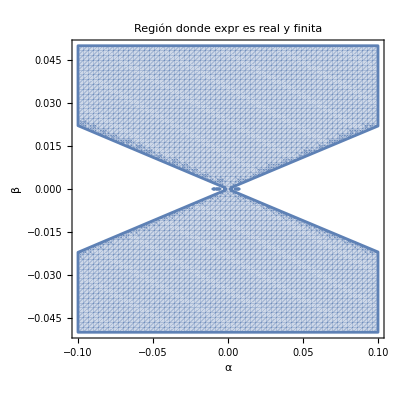

```mathematica
RegionPlot[Im[dem]==0&&dem!=0,{α,-0.1,0.1},{β,-0.05,0.05},PlotPoints->60,FrameLabel->{"α","β"},PlotLabel->"Región donde expr es real y finita"]
```

### Condiciones de singularidad

```mathematica
Prueba1:=-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3)
```

```mathematica
dem:=686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2)
```

```mathematica
Solve[dem==0,β]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{β→-1/6 √(7/3) α},{β→1/6 √(7/3) α}}

```mathematica
Assuming[r>0&& α>0 &&β>0,Simplify[Series[Simplify[Prueba1],{r,Infinity,1}]]]
```

((7 α+(7^(2/3) (7 α^2-108 β^2))/((49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3)) r^2)/(36 β^2)+1+O[1/r]^(4/3)

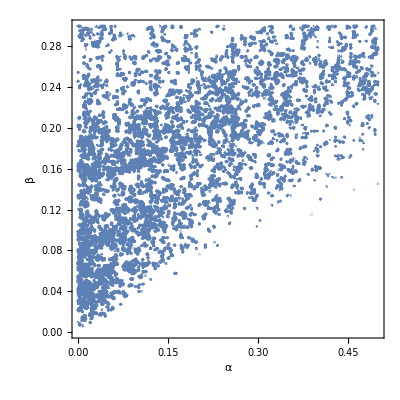

```mathematica
Assuming[r>0&& α>0 &&β>0,RegionPlot[7 α+(7^(2/3) (7 α^2-108 β^2))/((49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3)==0,{α,0,0.5},{β,0,0.3},PlotPoints->100,FrameLabel->{"α","β"}]]
```

### Invariante de Krhestmann

```mathematica
Khr[r_]:=Simplify[Sum[RiemDDDD[μ,ν,σ,γ]*RiemUUUU[μ,ν,σ,γ],{μ,0,len-1},{ν,0,len-1},{σ,0,len-1},{γ,0,len-1}]/.f[r]->fz3/.NN[r]->1/.NN'[r]->0/.NN''[r]->0/. f'[r]->D[fz3,r]/.f''[r]->D[fz3,{r,2}]]
```

```mathematica
ToRadicals[Khr[r]]
```

1/r^4 12 (-1-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))^2+(1176 (c-6 r^2+2 (3 r^2+α) (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))-α (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))^2)^2)/(21 r^4+14 r^2 α+36 α^2-2 α (7 r^2+36 α) (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))+36 α^2 (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))^2)^2+(2401 r^4 (288 c^2 α (35 r^2+18 α)+c (-89551 r^6-32676 r^4 α+180144 r^2 α^2+10368 α^3)+3 (62335 r^8+2436 r^6 α-10892 r^4 α^2+56688 r^2 α^3+1728 α^4)-(187005 r^8+193718 r^6 α-32676 r^4 α (c+α)+319968 r^2 α^2 (c+α)+5184 α^2 (c+α)^2) (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))+101 r^2 α (959 r^4+1584 α (c+α)) (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))^2)^2)/(5184 (21 r^4+14 r^2 α+36 α^2-2 α (7 r^2+36 α) (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))+36 α^2 (-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+((-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))/(36 2^(1/3) α^2))^2)^6)

```mathematica
R3=Collect[Simplify[c1*R31+c2*R32+c3*R33+c4*R34+c5*R35+c6*R36+c7*R37+c8*R38],{c1,c2,c3}]
```

1/54 c2 (54 R32-39 R34-336 R35-272 R36+372 R37-49 R38)+1/72 c1 (72 R31+3 R34-24 R35+32 R36-12 R37+R38)+1/81 c3 (81 R33-21 R34-2 (78 R35+67 R36-69 R37+8 R38))